```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/morning_sec_int_data/500nm.dat"]
```

{{1.12389,0.291848},{1.13423,0.29632},{1.14739,0.294236},{1.16401,0.29349},{1.183,0.301067},{1.20042,0.291325},{1.22646,0.285254},{1.24828,0.277404},{1.27782,0.272771},{1.30453,0.268499},{1.34407,0.264285},{1.38078,0.256888},{1.41705,0.246548},{1.46132,0.23246},{1.51023,0.218895},{1.58758,0.196717},{1.63065,0.190786}}

0.546277-0.215199 x

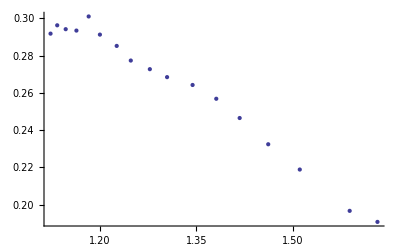

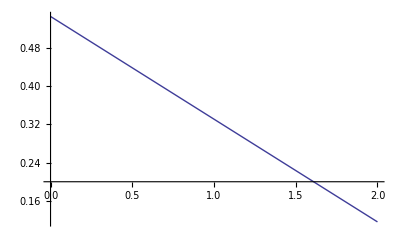

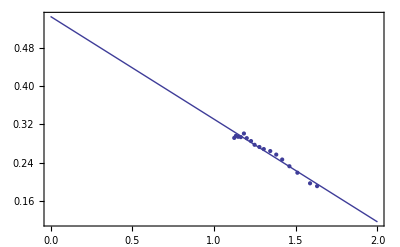

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```